```mathematica
(*This version has the joint offsets too*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nightmareforev/git/research/DIVA-R1.1.3-V/src/arc

```mathematica
<<rotationtools.wl
```

Starting with the given DH parameters with the global axis fixed at the joint 1 with x axis along the link and the angle of rotation about its z-axis

```mathematica
DH2HomTrans[aim1_, αim1_, di_, θi_]
```

```mathematica
(*T1 = Hom[rotZ[θ1], {0,0,0}];
T2 = Hom[rotY[-π/2], {0,0,0}];
T3 = Hom[rotZ[0], {a2,0,0}];
T4 = Hom[rotZ[θ2-(π/2)], {0,0,0}];
T5 = Hom[rotZ[0], {a3, 0, 0}];
T6 = Hom[rotY[π/2], {0,0,0}];
(*T6 = Hom[rotY[-π/2], {0,0,0}];*)
T7 = Hom[rotZ[θ3], {0, 0, 0}];
T8 = Hom[rotY[-π/2], {0,0,0}];
T9 = Hom[rotZ[0], {lua,0,0}];
T10 = Hom[rotX[-π/2], {0,0,0}];
T11 = Hom[rotZ[θ4], {0,0,0}];
T12 = Hom[rotZ[0], {a4, 0, 0}];
T13 = Hom[rotY[π/2], {0,0,0}];
T14 = Hom[rotZ[θ5], {0,0,0}];
T15 = Hom[rotY[-π/2], {0,0,0}];
T16 = Hom[rotZ[0], {lfa,0,0}];
T17 = Hom[rotZ[θ6], {0, 0, 0}];
T18 = Hom[rotX[π/2], {0, 0, 0}];
T19 = Hom[rotZ[θ7], {0, 0, 0}];
T20 = Hom[rotX[-π/2], {0, 0, 0}];
T21 = Hom[rotZ[0], {a5, 0, 0}];*)
```

```mathematica
T1 = Hom[rotZ[θ1], {0,0,0}];
T2 = Hom[rotY[-π/2], {0,0,0}];
T3 = Hom[rotZ[0], {a2,0,0}];
T4 = Hom[rotZ[-θ2-π/2], {0,0,0}];
T5 = Hom[rotY[π/2], {0,0,0}];
T6 = Hom[rotZ[0], {0, 0, a3}];
T7 = Hom[rotZ[θ3], {0, 0, 0}];
T8 = Hom[rotZ[0], {0,0,lua}];
T9 = Hom[rotY[θ4], {0,0,0}];
T10 = Hom[rotZ[0], {0, 0, a4}];
T11 = Hom[rotZ[θ5], {0,0,0}];
T12 = Hom[rotZ[0], {0,0,lfa}];
T13 = Hom[rotY[θ6], {0, 0, 0}];
T14 = Hom[rotX[θ7], {0, 0, 0}];
T15 = Hom[rotZ[0], {0, 0, a5}];
```

```mathematica
(*1, 5, 7, 9, 11, 13, 14, 15*)
```

```mathematica
(*Verifying the transformations with ADAM and pydrake -- Verified and works*)
θtestnew = Inner[Rule, θ, {-0.86,-0.67,-0.37,-1.64,-0.64,0.93,-0.61}, List];
fkto[15]/.θtestnew/.robotParams//MatrixForm
```

(-0.222141 | 0.688753 | -0.690125 | -0.366013
-0.963916 | -0.261625 | 0.0491654 | 0.0437754
-0.146691 | 0.676145 | 0.722018 | 0.456895
0 | 0 | 0 | 1)

```mathematica
(*Finding the FK of this robot and plotting the manipulator*)
robotParams = {a2->0.116, a3->0.09,  lua->0.25, a4->0.04, lfa->0.2,a5->0.1, d1->0.05, d2->0.05, d->0.02, ρ->2800};
```

```mathematica
(*The forward kinematics*)
Clear[i, fk]
fkto[num_]:=Module[{fk, i},
fk = T1;
For[i=2,i≤num,i++,
fk = fk.Symbol[ToString["T"<>ToString[i]]];
];
Return[fk];
];
```

```mathematica
(*Plotting the manipulator*)
θ = {θ1, θ2, θ3, θ4, θ5, θ6, θ7};
θtest = Inner[Rule, θ, {0,0,0,0,0,0, 0}, List];

allVars = Join[θ, {a2, a3, a4, a5, lua, lfa}];

basec1 = {0, 0, -0.03};
basec2 = {0, 0, 0.03};
basecr = 0.02;
basec = {0,0,0};
linkr = 0.01;
```

```mathematica
j1= Graphics3D[{Red, Cylinder[{basec1,basec2},basecr ]}];
l1 = Graphics3D[{Blue, Cylinder[{basec, basec+(fkto[3])[[;;3, -1]]}, linkr]}]/.robotParams;
j2= Graphics3D[{Red, Cylinder[Transpose[(fkto[5][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[5][[;;3,4]], fkto[7][[;;3,4]]},basecr ]}]/.robotParams;
l2= Graphics3D[{Blue, Cylinder[{fkto[5][[;;3,4]], fkto[7][[;;3,4]]},linkr ]}]/.robotParams;
j3= Graphics3D[{Red, Cylinder[Transpose[(fkto[7][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[7][[;;3,4]], fkto[7][[;;3,4]]},basecr ]}]/.robotParams;
l3= Graphics3D[{Blue, Cylinder[{fkto[7][[;;3,4]], fkto[9][[;;3,4]]},linkr ]}]/.robotParams;
j4= Graphics3D[{Red, Cylinder[Transpose[(fkto[9][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[11][[;;3,4]], fkto[11][[;;3,4]]},basecr ]}]/.robotParams;
l4= Graphics3D[{Blue, Cylinder[{fkto[9][[;;3,4]], fkto[11][[;;3,4]]},linkr ]}]/.robotParams;
j5= Graphics3D[{Red, Cylinder[Transpose[(fkto[11][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[13][[;;3,4]], fkto[14][[;;3,4]]},basecr ]}]/.robotParams;
l5= Graphics3D[{Blue, Cylinder[{fkto[11][[;;3,4]], fkto[13][[;;3,4]]},linkr ]}]/.robotParams;
j6= Graphics3D[{Red, Cylinder[Transpose[(fkto[13][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[14][[;;3,4]], fkto[17][[;;3,4]]},basecr ]}]/.robotParams;
j7= Graphics3D[{Red, Cylinder[Transpose[(fkto[14][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[15][[;;3,4]], fkto[19][[;;3,4]]},basecr ]}]/.robotParams;
l67= Graphics3D[{Blue, Cylinder[{fkto[14][[;;3,4]], fkto[15][[;;3,4]]},linkr ]}]/.robotParams;
```

```mathematica
range = 0.8;
robot = Show[j1, l1, j2, l2, j3, l3, j4, l4, j5, l5, j6, j7, l67, PlotRange->{{-range/1.5, range/1.5}, {-range, 0.2}, {0, range/1.5}}];
robottest = robot/.θtest;
```

```mathematica
eefCoords = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real}, {θ6, _Real}, {θ7, _Real}}, Evaluate[(fkto[21]/.robotParams)[[;;3, 4]]]];
fktrans = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real}, {θ6, _Real}, {θ7, _Real}}, Evaluate[(fkto[21]/.robotParams)]];
```

```mathematica
(*Dynamics*)
qt= {θ1[t], θ2[t], θ3[t], θ4[t], θ5[t], θ6[t], θ7[t]};
q= {θ1, θ2, θ3, θ4, θ5, θ6, θ7};
```

```mathematica
axis = Graphics3D[{{Red, Arrow[{{0,0,0}, {0.5, 0, 0}}]}, {Green, Arrow[{{0,0,0}, {0, 0.5, 0}}]}, {Blue, Arrow[{{0,0,0}, {0, 0, 0.5}}]}}];
```

```mathematica
pc1 = (fkto[2].Hom[rotZ[0], {a2/2,0,0}])[[;;3, 4]];
pc2 = (fkto[5].Hom[rotZ[0], {0,0,a3/2}])[[;;3,4]];
pc3 = (fkto[7].Hom[rotZ[0], {0,0,lua/2}])[[;;3,4]];
pc4 = (fkto[9].Hom[rotZ[0], {0,0,a4/2}])[[;;3,4]];
pc5 = (fkto[11].Hom[rotZ[0], {0,0,lfa/2}])[[;;3,4]];
pc6 = (fkto[14].Hom[rotZ[0], {0,0,a5/2}])[[;;3,4]];
pef = (fkto[21])[[;;3,4]];
```

```mathematica
com1 = Graphics3D[{Green, Sphere[pc1, 0.015]}];
com2 = Graphics3D[{Green, Sphere[pc2, 0.015]}];
com3 = Graphics3D[{Green, Sphere[pc3, 0.015]}];
com4 = Graphics3D[{Green, Sphere[pc4, 0.015]}];
com5 = Graphics3D[{Green, Sphere[pc5, 0.015]}];
com6 = Graphics3D[{Green, Sphere[pc6, 0.015]}];
coms = Show[com1, com2, com3, com4, com5, com6];
```

```mathematica
robocoords = Manipulate[Show[robot, coms, axis, PlotRange->All]/.robotParams/.{θ1->t1, θ2->t2, θ3->t3, θ4->t4, θ5->t5, θ6->t6, θ7->t7},{{t1,0},-π,π},{{t2,0},-π,π},{{t3,0},-π,π},{{t4,0},-π,π},{{t5,0},-π,π},{{t6,0},-π,π},{{t7,0},-π,π}]
```

```mathematica
(*Design domain for the link*)
```

```mathematica
Jv1 = D[pc1, {θ}];
Jv2 = D[pc2, {θ}];
Jv3 = D[pc3, {θ}];
Jv4 = D[pc4, {θ}];
Jv5 = D[pc5, {θ}];
Jv6 = D[pc6, {θ}];
Jef = D[pef, {θ}];
```

```mathematica
θtestnew = Inner[Rule, θ, {-1,-0.23,0.43,0.32,0,0,0}, List];
```

```mathematica
Jv2/.robotParams/.θtestnew//MatrixForm
```

(0.0236733 | -0.00863264 | 0 | 0 | 0 | 0 | 0
-0.036869 | -0.00554296 | 0 | 0 | 0 | 0 | 0
0 | -0.043815 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Design domain is a cuboid*)
```

```mathematica
(*pc1 = (fkto[2].Hom[rotZ[0], {a2/2,0,0}])[[;;3, 4]];
pc2 = (fkto[4].Hom[rotZ[0], {a3/2,0,0}])[[;;3,4]];
pc3 = (fkto[8].Hom[rotZ[0], {lua/2,0,0}])[[;;3,4]];
pc4 = (fkto[11].Hom[rotZ[0], {a4/2,0,0}])[[;;3,4]];
pc5 = (fkto[15].Hom[rotZ[0], {lfa/2,0,0}])[[;;3,4]];
pc6 = (fkto[20].Hom[rotZ[0], {a5/2,0,0}])[[;;3,4]];
pef = (fkto[21])[[;;3,4]];*)
```

```mathematica
R1 = (fkto[2].Hom[rotZ[0], {a2/2,0,0}])[[;;3, ;;3]]/.robotParams;
Jω1 = SkewMat2vec[Simplify[Transpose[R1].D[R1,{θ}]]];
R2 = (fkto[4].Hom[rotZ[0], {a3/2,0,0}])[[;;3,;;3]]/.robotParams;
Jω2 = SkewMat2vec[Simplify[Transpose[R2].D[R2,{θ}]]];
R3 = (fkto[8].Hom[rotZ[0], {lua/2,0,0}])[[;;3,;;3]]/.robotParams;
Jω3 = SkewMat2vec[Simplify[Transpose[R3].D[R3,{θ}]]];
R4 = (fkto[11].Hom[rotZ[0], {a4/2,0,0}])[[;;3,;;3]]/.robotParams;
Jω4 = SkewMat2vec[Simplify[Transpose[R4].D[R4,{θ}]]];
R5 = (fkto[15].Hom[rotZ[0], {lfa/2,0,0}])[[;;3,;;3]]/.robotParams;
Jω5 = SkewMat2vec[Simplify[Transpose[R5].D[R5,{θ}]]];
R6 = (fkto[20].Hom[rotZ[0], {a5/2,0,0}])[[;;3,;;3]]/.robotParams;
Jω6 = SkewMat2vec[Simplify[Transpose[R6].D[R6,{θ}]]];
Ref = (fkto[21])[[;;3,;;3]]/.robotParams;
Jωef = SkewMat2vec[Simplify[Transpose[Ref].D[Ref,{θ}]]];
```

```mathematica
Jef/.robotParams/.θtest//MatrixForm
```

(0.68 | 0. | 0. | 0.34 | 0. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0.68 | 0. | 0. | 0. | 0. | 0.1)

```mathematica
I1 = {{i11, 0, 0}, {0,i12, 0}, {0, 0,i13}};
I2 = {{i21, 0, 0}, {0,i22, 0}, {0, 0,i23}};
I3 = {{i31, 0, 0}, {0,i32, 0}, {0, 0,i33}};
I4 = {{i31, 0, 0}, {0,i32, 0}, {0, 0,i33}};
I5 = {{i31, 0, 0}, {0,i32, 0}, {0, 0,i33}};
I6 = {{i31, 0, 0}, {0,i32, 0}, {0, 0,i33}};
Ief = {{ie1, 0, 0}, {0,ie2, 0}, {0, 0,ie3}};
```

```mathematica
Mmat = Transpose[Jv1].Jv1*m1+Transpose[Jv2].Jv2*m2+Transpose[Jv3].Jv3*m3+Transpose[Jv4].Jv4*m4+Transpose[Jv5].Jv5*m5+Transpose[Jv6].Jv6*m6+Transpose[Jω1].I1.Jω1+Transpose[Jω2].I2.Jω2+Transpose[Jω3].I3.Jω3+Transpose[Jω4].I4.Jω4+Transpose[Jω5].I5.Jω5+Transpose[Jω6].I6.Jω6+Transpose[Jef].Jef*mef+Transpose[Jωef].Ief.Jωef;
Mmat//Dimensions
```

{7,7}

```mathematica
(Mmat - Transpose[Mmat])/Simplify
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

```mathematica
q2qt = Inner[Rule, q, qt, List];
M = Mmat/.q2qt;
n = Length[qt];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii = 1, ii ≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[M[[ii,jj]], qt[[kk]]] + D[M[[ii,kk]], qt[[jj]]] - D[M[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
```

```mathematica
tempC//Dimensions
```

{7,7}

```mathematica
dM = D[M, t];
```

```mathematica
(*Not the direction of gravity but just for the computation of the gravity potential*)
gvec = {0, g, 0};
V = (m1*pc1.gvec+m2*pc2.gvec+m3*pc3.gvec+m4*pc4.gvec+m5*pc5.gvec+m6*pc6.gvec+mef*pef.gvec);
G = D[V, {θ}];
LHS = (Mmat/.q2qt).D[qt, {t, 2}]+(tempC).D[qt, t]+(G/.q2qt);
```

```mathematica
masses = {m1-> ρ*π*d^2/4*a2, m2-> ρ*π*d^2/4*a3, m3-> ρ*π*d^2/4*lua, m4-> ρ*π*d^2/4*a4, m5-> ρ*π*d^2/4*lfa, m6-> ρ*π*d^2/4*a5, mef->1}/.robotParams;
inertias = {i11->1/2*m1*a2^2,i12->1/12*m1*(a2^2+3*d^2/4), i13->1/12*m1*(a2^2+3*d^2/4),
	      i21->1/2*m2*a3^2,i22->1/12*m2*(a3^2+3*d^2/4), i23->1/12*m2*(a3^2+3*d^2/4),
               i31->1/2*m3*lua^2,i32->1/12*m3*(lua^2+3*d^2/4), i33->1/12*m3*(lua^2+3*d^2/4),
               i41->1/2*m4*a4^2,i42->1/12*m4*(a4^2+3*d^2/4), i43->1/12*m4*(a4^2+3*d^2/4),
               i51->1/2*m5*lfa^2,i52->1/12*m5*(lfa^2+3*d^2/4), i53->1/12*m5*(lfa^2+3*d^2/4),
               i61->1/2*m6*a5^2,i62->1/12*m6*(a5^2+3*d^2/4), i63->1/12*m6*(a5^2+3*d^2/4),
ie1->0,ie2->0, ie3->0}/.masses/.robotParams; (*The end-effector is considered to carry a point mass, hence no inertia*)
```

```mathematica
numdata = Join[robotParams, masses,inertias,  {g->9.81}];
qt2q = Map[Reverse, q2qt];
```

```mathematica
cM = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real}, {θ6, _Real}, {θ7, _Real}},Evaluate[M/.qt2q/.numdata]];
dθ = Inner[Rule, D[qt,{t}],{dθ1, dθ2, dθ3, dθ4, dθ5, dθ6, dθ7}, List];
cC = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real},{θ5, _Real}, {θ6, _Real}, {θ7, _Real},  {dθ1, _Real}, {dθ2, _Real}, {dθ3, _Real}, {dθ4, _Real}, {dθ5, _Real}, {dθ6, _Real}, {dθ7, _Real}},Evaluate[tempC/.qt2q/.numdata/.dθ]];
cG = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real},{θ5, _Real}, {θ6, _Real}, {θ7, _Real}},Evaluate[G/.numdata]];
```

```mathematica
(*Now formulating the RHS terms*)
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval},
Mval=cM@@q;
Cval=cC@@Join[q, dq];
Gval=cG@@q;

Return[-Inverse[Mval].(Cval.dq+Gval)];
];
```

```mathematica
tf=10;
dynsim = NDSolve[{doubledots[z[t],z'[t]]==z''[t],z[0]=={0.1,-0.1,0.2,0.33,0.45,-0.3,0.1},z'[0]=={0,0,0,0,0,0,0}},z,{t,0,tf}][[1]][[1]];
```

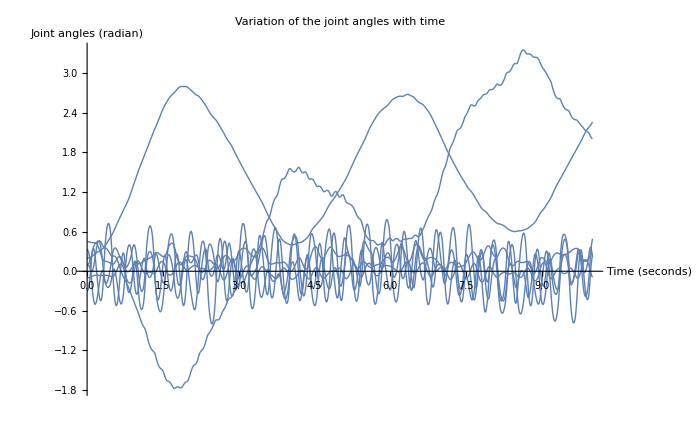

```mathematica
Plot[Evaluate[{z[t]}/.dynsim],{t,0,tf}, PlotRange-> All, PlotStyle->Thick, LabelStyle->Directive[Bold,Black,15], AxesLabel-> {"Time (seconds)","Joint angles (radian)"}, PlotLabel->"Variation of the joint angles with time",ImageSize->700]
```

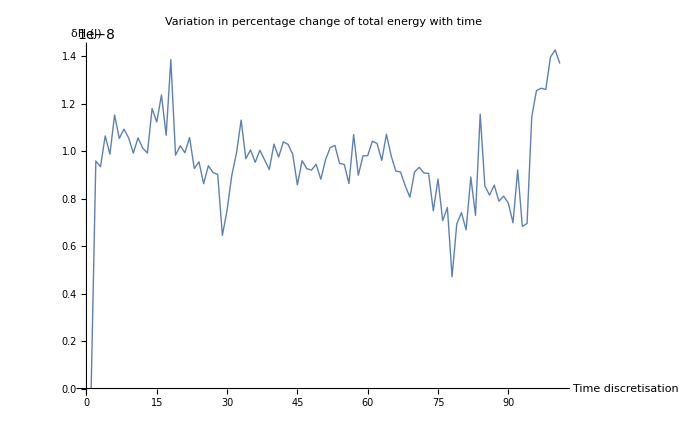

```mathematica
qdot = D[qt,t];
T = 1/2 *qdot.M.qdot;

H = T+(V/.q2qt);
δH = (H/(H/.{t-> 0})-1)*100/.numdata;
cH = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real},{θ5, _Real}, {θ6, _Real}, {θ7, _Real},  {dθ1, _Real}, {dθ2, _Real}, {dθ3, _Real}, {dθ4, _Real}, {dθ5, _Real}, {dθ6, _Real}, {dθ7, _Real}},Evaluate[H/.numdata/.dθ/.qt2q]];
Hi = cH@@Flatten[Join[{z[t]},{D[z[t], t]}]/.dynsim/.t->0];
ListLinePlot[Table[((cH@@Flatten[Join[{z[t]},{D[z[t], t]}]/.dynsim/.t->ii])/Hi)-1,{ii, 0, 10, 0.1}], PlotStyle->Thick, LabelStyle->Directive[Bold,Black,15], AxesLabel-> {"Time discretisation","δH (J)"}, PlotLabel->"Variation in percentage change of total energy with time",ImageSize->700]
```

```mathematica
Manipulate[robot/.Inner[Rule, θ, (z[t]/.dynsim/.t->u), List],{u, 0, 10}]
```

ReplaceAll::reps: {dynsim} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::normal: Nonatomic expression expected at position 2 in Inner[Rule,θ,z[0]/.dynsim,List].

ReplaceAll::reps: {Inner[Rule,θ,z[0]/.dynsim,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
fk@@ {-0.8835452772493956,0.4025493193142002,-0.024400395278256742,1.0094098779394565,0.10490600736636944,0.2537500708621454,-0.5658390141485352}//MatrixForm
```

fk[-0.883545,0.402549,-0.0244004,1.00941,0.104906,0.25375,-0.565839]

```mathematica
(*Now lets implement feedback linearisation*)
(*There is no reference trajectory here, there is only a reference pose to reach*)
(*qr = {0.1,-0.1,0.2,0.33,0.45,-0.3,0.1};*)
qr = {-0.8835452772493956,0.4025493193142002,-0.024400395278256742,1.0094098779394565,0.10490600736636944,0.2537500708621454,-0.5658390141485352};
dqr = {0,0,0,0,0,0,0};
d2qr = {0,0,0,0,0,0,0};
```

```mathematica
(*Control gains, keeping them same for all the joints*)
Kp = 10;
Kd = 2*Sqrt[Kp];
τmax = {1,1,1,1,1,1,1};
```

```mathematica
(*Now formulating the RHS terms*)
Clear[τapplied, tapplied, controlfl]
τapplied = {};
tapplied = {};
controlfl[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&), t_]:=Module[{Mval, Cval, Gval, τval, τdash},
Mval=cM@@q;
Cval=cC@@Join[q, dq];
Gval=cG@@q;

τdash = d2qr+Kd*IdentityMatrix[7].(dqr-dq)+Kp*IdentityMatrix[7].(qr-q);
τval = Mval.τdash+Cval.dq+Gval;
AppendTo[τapplied, τval];
AppendTo[tapplied, t];

Return[Inverse[Mval].(τval-Cval.dq-Gval)];
];
```

```mathematica
fk@@{-0.2382318277503335,0.38289237996528763,0.0505952793852708,1.424616394774079,-0.022455120342545445,0.5966584034460232,-0.0036553135306927097}//MatrixForm
```

fk[-0.238232,0.382892,0.0505953,1.42462,-0.0224551,0.596658,-0.00365531]

```mathematica
dintsol = DSolve[{x''[t]+2Sqrt[kp]*x'[t]+x[t]==0, x[0]==A, x'[0]==0},x[t], t][[1]];
```

```mathematica
eqn = x[t]/.dintsol//FullSimplify
```

(A ⅇ^(-√kp t) (√(-1+kp) Cosh[√(-1+kp) t]+√kp Sinh[√(-1+kp) t]))/(√(-1+kp))

```mathematica
eqn
```

(A ⅇ^(-√kp t) (√(-1+kp) Cosh[√(-1+kp) t]+√kp Sinh[√(-1+kp) t]))/(√(-1+kp))

```mathematica
tf=10;
controlsim = NDSolve[{controlfl[z[t],z'[t], t]==z''[t],z[0]=={-0.2382318277503335,0.38289237996528763,0.0505952793852708,1.424616394774079,-0.022455120342545445,0.5966584034460232,-0.0036553135306927097},z'[0]=={0,0,0,0,0,0,0}},z,{t,0,tf}, Method->"Adams"][[1]][[1]];
```

```mathematica
configs = Table[z[t]/.controlsim/.t->2,{t, 0, tf, 0.01}];
endpts = Table[eefCoords@@configs[[i]],{i, 1, Length[configs]}];
```

```mathematica
Manipulate[Show[robot/.Inner[Rule, θ,configs[[u]], List], Graphics3D[{Black, Sphere[endpts[[;;u]], 0.01]}], Graphics3D[{Green, Sphere[endpts[[1]], 0.03]}], Graphics3D[{Red, Sphere[endpts[[-1]], 0.03]}]],{u, 1,Length[endpts], 1}]
```

Part::partd: Part specification configs⟦1⟧ is longer than depth of object.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{θ1,θ2,θ3,θ4,θ5,θ6,θ7},configs⟦1⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 1 through 1 in endpts.

Part::partd: Part specification endpts⟦1⟧ is longer than depth of object.

Part::partd: Part specification endpts⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[/.Inner[Rule,{θ1,θ2,θ3,θ4,θ5,θ6,θ7},configs⟦1⟧,List],,,].

Part::partd: Part specification configs⟦1⟧ is longer than depth of object.

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{θ1,θ2,θ3,θ4,θ5,θ6,θ7},configs⟦1⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::take: Cannot take positions 1 through 1 in endpts.

Part::partd: Part specification endpts⟦1⟧ is longer than depth of object.

Part::partd: Part specification endpts⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[/.Inner[Rule,{θ1,θ2,θ3,θ4,θ5,θ6,θ7},configs⟦1⟧,List],,,].

```mathematica
(*Visualise trajectory*)
```

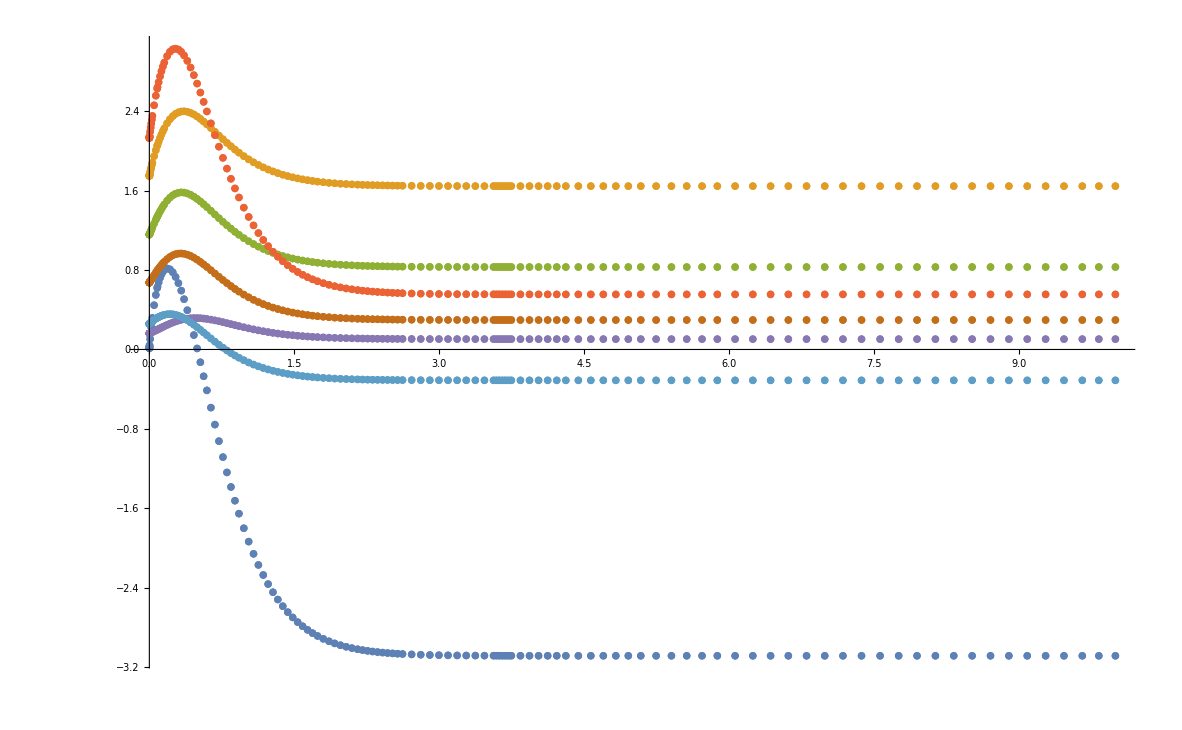

```mathematica
(*From this we can compute the settling time*)
ListPlot[Table[Transpose[{tapplied,τapplied[[;;,i]]}],{i, Dimensions[τapplied][[2]]}], PlotRange->All]
```

```mathematica
Max[Abs[τapplied]]
```

3.08729

```mathematica
G/.numdata/.{θ1->0,θ2->π/2,θ3->0,θ4->0,θ5->0,θ6->0,θ7->0}/.g->9.81
```

{-0.783897,8.6659,0.,0.,0.,0.,1.02415}

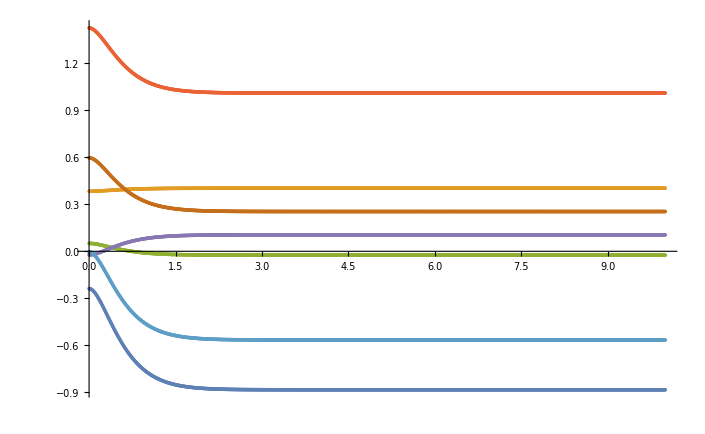

```mathematica
qvals = Table[z[t]/.controlsim/.t->ii,{ii, 0, tf, 0.01}];
timesamples = Table[t, {t, 0, tf, 0.01}];
ListPlot[Table[Transpose[{timesamples,qvals[[;;,i]]}],{i, Dimensions[τapplied][[2]]}]]
```

```mathematica
Max[Abs[qvals]]
Max[Abs[qr]]
```

1.42462

1.00941

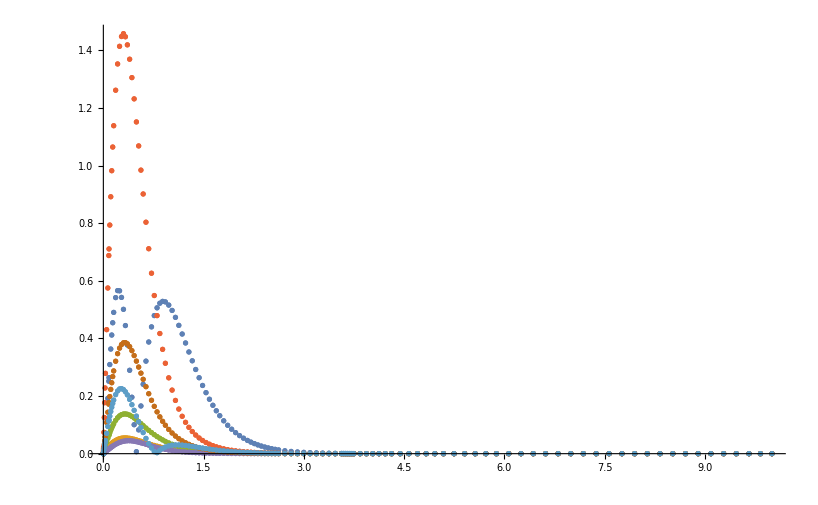

```mathematica
dqapplied = Table[D[z[t], t]/.controlsim/.t->tapplied[[tt]], {tt, Length[tapplied]}];
(*Power at each joint*)
powapplied = Table[τapplied[[i]]*dqapplied[[i]],{i, Length[τapplied]}];
ListPlot[Table[Transpose[{tapplied,Abs[powapplied[[;;,i]]]}],{i, Dimensions[powapplied][[2]]}], PlotRange->All]
```

```mathematica
Max[powapplied]
```

0.528748

```mathematica
(*Simulate torque limit here first*)
(*If we dont apply a max torque limit, we can use the analytical formulae to estimate the settling time. So τmax can be treated at the qoi rather than at the dvs*)
(*Lets also further simplify by sampling Kd based on Kp to make the motion overdamped*)
```

```mathematica
(*Now port the details into C++ and see if we can do the simulations, but do we need to do the simulation?*)
```

```mathematica
(*Settling time*)
```

```mathematica
8/Kd//N
```

1.26491

```mathematica
temp = z[t]/.controlsim/.t->8/Kd
```

{-0.824449,0.400749,-0.0175324,1.04743,0.0932425,0.285153,-0.514355}

```mathematica
(temp - qr)/qr*100
```

{-6.68858,-0.447187,-28.147,3.76694,-11.118,12.3755,-9.09866}

```mathematica
(*Settling time is done*)
```

```mathematica
(*The way I am dealing with it, any robot can move from one position in joint space to another and there is no unique design/desgin space to isolate*)
```

To make this exercise any meaningful, we need some meaningful requirements
1. Settling time (Just effected by control) (Can be written in Py)
2. Torque required (Effected by control and mechanics) (Need to implement dynamics in CPP)
3. Kinematic/workspace requirements to reach the final position(R^3)/pose (SE^3) (Effected by the mechanics) (IK computation) (Need to implement IK in CPP)
4. Static load cases for feasibility (Effected by the control and mechanics) (Can be written in Py)
5. Static load cases for deflection (Effected by the control and mechanics) (Who would evaluate the effect of the stiffness/ who would compute the end-effector deflection under load?)
6. Maximum power at the joint (Effected by control and mechanics) (Can be written in Py)

7. Need  a check for self-collision while blindly moving with joint space planning
8. Need a check for collision with obstacles

Other way is to just define 20 poses and say all the robots should be able to reach these poses and also be able to carry a load through these poses, this we could do in the next step where we can also define the path of the robot

```mathematica
(*(*For the torques at static locations, G can be used, which is the torque required at a stationary location and the solution for the statics problem*)
G/.{θ1->0,θ2->π/2,θ3->0,θ4->0,θ5->0,θ6->0,θ7->0}/.numdata*)
```

```mathematica
θ2th = Inner[Rule, θ, {th1, th2, th3, th4, th5, th6, th7}, List];
```

```mathematica
csrule = {Cos[θ1]->c1,Cos[θ2]->c2,Cos[θ3]->c3,Cos[θ4]->c4,Cos[θ5]->c5,Cos[θ6]->c6,Cos[θ7]->c7, Sin[θ1]->s1,Sin[θ2]->s2,Sin[θ3]->s3,Sin[θ4]->s4,Sin[θ5]->s5,Sin[θ6]->s6,Sin[θ7]->s7, Sin[θ1[t]]->s1,Sin[θ2[t]]->s2,Sin[θ3[t]]->s3,Sin[θ4[t]]->s4,Sin[θ5[t]]->s5,Sin[θ6[t]]->s6,Sin[θ7[t]]->s7, Cos[θ1[t]]->c1,Cos[θ2[t]]->c2,Cos[θ3[t]]->c3,Cos[θ4[t]]->c4,Cos[θ5[t]]->c5,Cos[θ6[t]]->c6,Cos[θ7[t]]->c7, θ1'[t]->dth1,θ2'[t]->dth2,θ3'[t]->dth3,θ4'[t]->dth4,θ5'[t]->dth5,θ6'[t]->dth6,θ7'[t]->dth7};
```

```mathematica
(*Reverse[csrule, {2}]*)
```

```mathematica
(*(*exporting the mass matrix*)
diagM = DiagonalMatrix[Diagonal[(Mmat/.csrule)]];
upperM = UpperTriangularize[(Mmat/.csrule)];*)
```

```mathematica
(*CForm[Flatten[diagM]]/.Power->pow;*)
```

```mathematica
(*(*Verifying the triangularisation*)
Simplify[-DiagonalMatrix[diagM]+upperM+Transpose[upperM]-(Mmat/.csrule)]*)
```

```mathematica
(*(*exporting the C matrix*)
CtoC = tempC/.csrule;*)
```

```mathematica
(*CForm[Flatten[CtoC]]/.Power->pow;*)
```

```mathematica
(*(*exporting the G vector*)
GtoC = G/.csrule;*)
```

```mathematica
(*CForm[Flatten[GtoC]]/.Power->pow;*)
```

```mathematica
(*CtoC/.csrule//Variables*)
```

```mathematica
(*Mmat/.numdata/.{θ1->1,θ2->2,θ3->3,θ4->4,θ5->5,θ6->6,θ7->7}//MatrixForm*)
```

```mathematica
(*tempC/.numdata/.{θ1[t]->1,θ2[t]->2,θ3[t]->3,θ4[t]->4,θ5[t]->5,θ6[t]->6,θ7[t]->7}/.{θ1'[t]->1,θ2'[t]->2,θ3'[t]->3,θ4'[t]->4,θ5'[t]->5,θ6'[t]->6,θ7'[t]->7}//MatrixForm*)
```

```mathematica
(*G/.numdata/.{θ1->1,θ2->2,θ3->3,θ4->4,θ5->5,θ6->6,θ7->7}*)
```

```mathematica
(*All the expressions are computed with decent accuracy. Will have to setup control simulation and parallelisation in CPP and then an interface between the CPP code and G7 python code*)
```

```mathematica
(*Tomorrow first thing lets setup IK in python and check its speed, if its superfast we can directly leave it in python*)
```

```mathematica
G/.{θ1->0,θ2->π/2,θ3->0,θ4->0,θ5->0,θ6->0,θ7->0}/.mef->1/.numdata
```

{-0.783897,8.6659,0,0,0,0,1.02415}

```mathematica
Table[MinMax[τapplied[[;;,i]]],{i, 7}]
```

{{-3.08729,0.816825},{1.64632,2.40013},{0.830929,1.58308},{0.555057,3.0318},{0.104362,0.316272},{0.296804,0.96758},{-0.311135,0.35643}}

```mathematica
(*We need an IK module now*)
```

```mathematica
fk = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real},  {θ6, _Real}, {θ7, _Real}},Evaluate[fkto[21]/.robotParams]] ;
dfk = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real},  {θ6, _Real}, {θ7, _Real}},Evaluate[D[(fkto[21]/.robotParams)[[;;3,4]], {{θ1, θ2, θ3, θ4, θ5, θ6, θ7}}]]] ;
```

```mathematica
fkto[21]/.θtest/.numdata//MatrixForm
```

(0 | 1 | 0 | -0.05
-1 | 0 | 0 | -0.68
0 | 0 | 1 | 0.166
0 | 0 | 0 | 1)

```mathematica
α = 0.5; (*Damping coefficient*)
pval = {0.2, -0.34, 0.3};
qtemp = {0,0,0,0,0,0,0};
loopcount= 0;
While[ loopcount≤2500 && Norm[pval-(fk@@qtemp)[[;;3,4]]]≥10^-5,
Jval = dfk@@qtemp;
δ = pval-(fk@@qtemp)[[;;3,4]];
qtemp = qtemp+α*Transpose[Jval].δ;
loopcount = loopcount+1;
]
```

```mathematica
dfk@@{1,2,3,4,5,6,7}//MatrixForm
```

(-0.153431 | -0.181257 | -0.129339 | 0.00768486 | 0.0328204 | -0.0290307 | -0.0305255
0.146782 | 0.116384 | 0.233463 | 0.184522 | -0.0605026 | 0.0648282 | 0.0223982
0. | 0.0406137 | -0.107538 | 0.258322 | -0.00472307 | -0.0252628 | 0.0925555)

```mathematica
qtemp = {1.13965,1.34754,1.09455,-1.89162,-0.125211,0.209612,-0.179587}
(fk@@qtemp)[[;;3,4]]
```

{1.13965,1.34754,1.09455,-1.89162,-0.125211,0.209612,-0.179587}

{0.200002,-0.340008,0.300004}

```mathematica
Show[robot, coms, axis, PlotRange->All]/.robotParams/.Inner[Rule, θ, qtemp, List]
```

-Graphics3D-

```mathematica
fkto[21]/.numdata/.{θ1->1,θ2->2,θ3->3,θ4->4,θ5->5,θ6->6,θ7->7}//N//MatrixForm
```

(0.870941 | -0.385072 | -0.305255 | 0.146782
0.458695 | 0.859902 | 0.223982 | 0.153431
0.17624 | -0.335094 | 0.925555 | 0.331405
0. | 0. | 0. | 1.)

```mathematica
FullSimplify[fkto[21][[;;3,4]]/.csrule]//CForm
```

```mathematica
Flatten[Evaluate[D[(fkto[21])[[;;3,4]], {θ}]]/.csrule]//CForm;
```

```mathematica
D[(fkto[21])[[;;3,4]], {θ}]/.csrule//CForm;
```

```mathematica
dfk@@{1,2,3,4,5,6,7}//MatrixForm
```

(-0.153431 | -0.181257 | -0.129339 | 0.00768486 | 0.0328204 | -0.0290307 | -0.0305255
0.146782 | 0.116384 | 0.233463 | 0.184522 | -0.0605026 | 0.0648282 | 0.0223982
0. | 0.0406137 | -0.107538 | 0.258322 | -0.00472307 | -0.0252628 | 0.0925555)

## Verifying the solution spaces

```mathematica
dv = {a2, a3, lua, a4, lfa, a5, d1, d2, ρ, d, Kv, τmaxv}
```

{a2,a3,lua,a4,lfa,a5,d1,d2,ρ,d,Kv,τmaxv}

```mathematica
temprule = Inner[Rule, dv, {0.1842,0.2036, 0.2610, 0.1036, 0.2054, 0.1232,0.0144,0.0360,3139.45, 0.049, 54.097, 2.67}, List]
```

{a2→0.1842,a3→0.2036,lua→0.261,a4→0.1036,lfa→0.2054,a5→0.1232,d1→0.0144,d2→0.036,ρ→3139.45,d→0.049,Kv→54.097,τmaxv→2.67}

```mathematica
tempm = {m1-> ρ*π*d^2/4*a2, m2-> ρ*π*d^2/4*a3, m3-> ρ*π*d^2/4*lua, m4-> ρ*π*d^2/4*a4, m5-> ρ*π*d^2/4*lfa, m6-> ρ*π*d^2/4*a5, mef->1}/.temprule
```

{m1→1.0905,m2→1.20535,m3→1.54517,m4→0.613332,m5→1.21601,m6→0.729367,mef→1}

```mathematica
G/.tempm/.temprule/.{θ1->0,θ2->π/2,θ3->0,θ4->0,θ5->0,θ6->0,θ7->0}/.g->9.81
```

{-0.891267,32.1519,0.,0.,0.,0.,1.64935}

```mathematica
(4/ts)^2
```

16/ts^2

```mathematica
qstart = {-0.2382318277503335,0.38289237996528763,0.0505952793852708,1.424616394774079,-0.022455120342545445,0.5966584034460232,-0.0036553135306927097};
```

```mathematica
einit = qr-qstart
```

{-0.645313,0.0196569,-0.0749957,-0.415207,0.127361,-0.342908,-0.562184}

```mathematica
NDSolve[{controlfl[z[t],z'[t], t]==z''[t],z[0]=={-0.2382318277503335,0.38289237996528763,0.0505952793852708,1.424616394774079,-0.022455120342545445,0.5966584034460232,-0.0036553135306927097},z'[0]=={0,0,0,0,0,0,0}},z,{t,0,tf}, Method->"Adams"][[1]][[1]];
```

```mathematica
numdata
```

{a2→0.116,a3→0.09,lua→0.25,a4→0.04,lfa→0.2,a5→0.1,d1→0.05,d2→0.05,d→0.02,ρ→2800,m1→0.102039,m2→0.0791681,m3→0.219911,m4→0.0351858,m5→0.175929,m6→0.0879646,mef→1,i11→0.000686518,i12→0.000116971,i13→0.000116971,i21→0.000320631,i22→0.0000554177,i23→0.0000554177,i31→0.00687223,i32→0.00115087,i33→0.00115087,i41→0.0000281487,i42→5.57109×10^-6,i43→5.57109×10^-6,i51→0.00351858,i52→0.000590829,i53→0.000590829,i61→0.000439823,i62→0.0000755029,i63→0.0000755029,ie1→0,ie2→0,ie3→0,g→9.81}

```mathematica
robotParams
```

{a2→0.116,a3→0.09,lua→0.25,a4→0.04,lfa→0.2,a5→0.1,d1→0.05,d2→0.05,d→0.02,ρ→2800}

```mathematica
(*Whats left is computing the max torque for the motion and max power, since error in tracking doesnt make any sense anymore*)
```

```mathematica
(*Plan is to integrate the double integrator with the initial and final positions in joint space and then use those values to compute the max tau and omega*)
```

```mathematica
Mmat/.csrule//Flatten;
```

```mathematica
D[eqn, t]//FullSimplify
```

-(A ⅇ^(-√kp t) Sinh[√(-1+kp) t])/(√(-1+kp))

```mathematica
Flatten[Mmat/.csrule];
```

## Sampling designs from the computed solution space

```mathematica
ssample = {RandomReal[{0.07, 0.177}], RandomReal[{0.0595, 0.157}], RandomReal[{0.1845, 0.251}], RandomReal[{0.05, 0.199}], RandomReal[{0.1, 0.153}], RandomReal[{0.1, 0.174}], RandomReal[{-0.05, 0}], RandomReal[{-0.05, 0.02}], RandomReal[{1000, 3670}], RandomReal[{0.005, 0.017}], RandomReal[{10, 28}], RandomReal[{8.85, 11.58}]};
ssrule = Inner[Rule, dv, ssample, List]

range = 0.8;
robot = Show[j1, l1, j2, l2, j3, l3, j4, l4, j5, l5, j6, j7, l67, PlotRange->{{-range/1.5, range/1.5}, {-range, 0.2}, {0, range/1.5}}]/.ssrule;
robottest = robot/.θtest
```

{a2→0.0943467,a3→0.0667444,lua→0.207785,a4→0.10192,lfa→0.102385,a5→0.163974,d1→-0.038169,d2→-0.0000757798,ρ→2553.96,d→0.00860332,Kv→19.922,τmaxv→10.1522}

-Graphics3D-

```mathematica
ssmasses = {m1-> ρ*π*d^2/4*a2, m2-> ρ*π*d^2/4*a3, m3-> ρ*π*d^2/4*lua, m4-> ρ*π*d^2/4*a4, m5-> ρ*π*d^2/4*lfa, m6-> ρ*π*d^2/4*a5, mef->1}/.ssrule;
ssinertias = {i11->1/2*m1*a2^2,i12->1/12*m1*(a2^2+3*d^2/4), i13->1/12*m1*(a2^2+3*d^2/4),
	      i21->1/2*m2*a3^2,i22->1/12*m2*(a3^2+3*d^2/4), i23->1/12*m2*(a3^2+3*d^2/4),
               i31->1/2*m3*lua^2,i32->1/12*m3*(lua^2+3*d^2/4), i33->1/12*m3*(lua^2+3*d^2/4),
               i41->1/2*m4*a4^2,i42->1/12*m4*(a4^2+3*d^2/4), i43->1/12*m4*(a4^2+3*d^2/4),
               i51->1/2*m5*lfa^2,i52->1/12*m5*(lfa^2+3*d^2/4), i53->1/12*m5*(lfa^2+3*d^2/4),
               i61->1/2*m6*a5^2,i62->1/12*m6*(a5^2+3*d^2/4), i63->1/12*m6*(a5^2+3*d^2/4),
ie1->0,ie2->0, ie3->0}/.ssmasses/.ssrule; (*The end-effector is considered to carry a point mass, hence no inertia*)
```

ReplaceAll::reps: {ssrule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{m1→1/4 a2 d^2 π ρ,m2→1/4 a3 d^2 π ρ,m3→1/4 d^2 lua π ρ,m4→1/4 a4 d^2 π ρ,m5→1/4 d^2 lfa π ρ,m6→1/4 a5 d^2 π ρ,mef→1}/.ssrule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ssrule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
ssnumdata = Join[ssrule, ssmasses,ssinertias,  {g->9.81}];
```

```mathematica
j1= Graphics3D[{Red, Cylinder[{basec1,basec2},basecr ]}];
l1 = Graphics3D[{Blue, Cylinder[{basec, basec+(fkto[3])[[;;3, -1]]}, linkr]}];
j2= Graphics3D[{Red, Cylinder[Transpose[(fkto[4][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[4][[;;3,4]], fkto[4][[;;3,4]]},basecr ]}];
l2= Graphics3D[{Blue, Cylinder[{fkto[4][[;;3,4]], fkto[7][[;;3,4]]},linkr ]}];
j3= Graphics3D[{Red, Cylinder[Transpose[(fkto[7][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[7][[;;3,4]], fkto[7][[;;3,4]]},basecr ]}];
l3= Graphics3D[{Blue, Cylinder[{fkto[7][[;;3,4]], fkto[10][[;;3,4]]},linkr ]}];
j4= Graphics3D[{Red, Cylinder[Transpose[(fkto[11][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[11][[;;3,4]], fkto[11][[;;3,4]]},basecr ]}];
l4= Graphics3D[{Blue, Cylinder[{fkto[11][[;;3,4]], fkto[13][[;;3,4]]},linkr ]}];
j5= Graphics3D[{Red, Cylinder[Transpose[(fkto[14][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[14][[;;3,4]], fkto[14][[;;3,4]]},basecr ]}];
l5= Graphics3D[{Blue, Cylinder[{fkto[14][[;;3,4]], fkto[17][[;;3,4]]},linkr ]}];
j6= Graphics3D[{Red, Cylinder[Transpose[(fkto[17][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[17][[;;3,4]], fkto[17][[;;3,4]]},basecr ]}];
j7= Graphics3D[{Red, Cylinder[Transpose[(fkto[19][[;;3,;;3]]).Transpose[{basec1, basec2}]]+{fkto[19][[;;3,4]], fkto[19][[;;3,4]]},basecr ]}];
l67= Graphics3D[{Blue, Cylinder[{fkto[19][[;;3,4]], fkto[21][[;;3,4]]},linkr ]}];
```

```mathematica
cM = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real}, {θ6, _Real}, {θ7, _Real}},Evaluate[M/.qt2q/.ssnumdata]];
dθ = Inner[Rule, D[qt,{t}],{dθ1, dθ2, dθ3, dθ4, dθ5, dθ6, dθ7}, List];
cC = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real},{θ5, _Real}, {θ6, _Real}, {θ7, _Real},  {dθ1, _Real}, {dθ2, _Real}, {dθ3, _Real}, {dθ4, _Real}, {dθ5, _Real}, {dθ6, _Real}, {dθ7, _Real}},Evaluate[tempC/.qt2q/.ssnumdata/.dθ]];
cG = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real},{θ5, _Real}, {θ6, _Real}, {θ7, _Real}},Evaluate[G/.ssnumdata]];
```

ReplaceAll::reps: {qt2q} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[ssrule,{m1→1/4 a2 d^2 π ρ,m2→1/4 a3 d^2 π ρ,m3→1/4 d^2 lua π ρ,m4→1/4 a4 d^2 π ρ,m5→1/4 d^2 lfa π ρ,m6→1/4 a5 d^2 π ρ,mef→1}/.ssrule,{i11→1/2 Power[«2»] m1,i12→1/12 Plus[«2»] m1,i13→1/12 Plus[«2»] m1,i21→1/2 Power[«2»] m2,i22→1/12 Plus[«2»] m2,i23→1/12 Plus[«2»] m2,i31→1/2 Power[«2»] m3,i32→1/12 Plus[«2»] m3,i33→1/12 Plus[«2»] m3,i41→1/2 Power[«2»] m4,«11»}/.({m1→Times[«5»],m2→Times[«5»],m3→Times[«5»],m4→Times[«5»],m5→Times[«5»],m6→Times[«5»],mef→1}/.ssrule)/.ssrule,{g→9.81}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qt2q} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[ssrule,{m1→1/4 a2 d^2 π ρ,m2→1/4 a3 d^2 π ρ,m3→1/4 d^2 lua π ρ,m4→1/4 a4 d^2 π ρ,m5→1/4 d^2 lfa π ρ,m6→1/4 a5 d^2 π ρ,mef→1}/.ssrule,{i11→1/2 Power[«2»] m1,i12→1/12 Plus[«2»] m1,i13→1/12 Plus[«2»] m1,i21→1/2 Power[«2»] m2,i22→1/12 Plus[«2»] m2,i23→1/12 Plus[«2»] m2,i31→1/2 Power[«2»] m3,i32→1/12 Plus[«2»] m3,i33→1/12 Plus[«2»] m3,i41→1/2 Power[«2»] m4,«11»}/.({m1→Times[«5»],m2→Times[«5»],m3→Times[«5»],m4→Times[«5»],m5→Times[«5»],m6→Times[«5»],mef→1}/.ssrule)/.ssrule,{g→9.81}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*Now formulating the RHS terms*)
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval},
Mval=cM@@q;
Cval=cC@@Join[q, dq];
Gval=cG@@q;

Return[-Inverse[Mval].(Cval.dq+Gval)];
];
```

```mathematica
tf=10;
dynsim = NDSolve[{doubledots[z[t],z'[t]]==z''[t],z[0]=={0.1,-0.1,0.2,0.33,0.45,-0.3,0.1},z'[0]=={0,0,0,0,0,0,0}},z,{t,0,tf}][[1]][[1]];
```

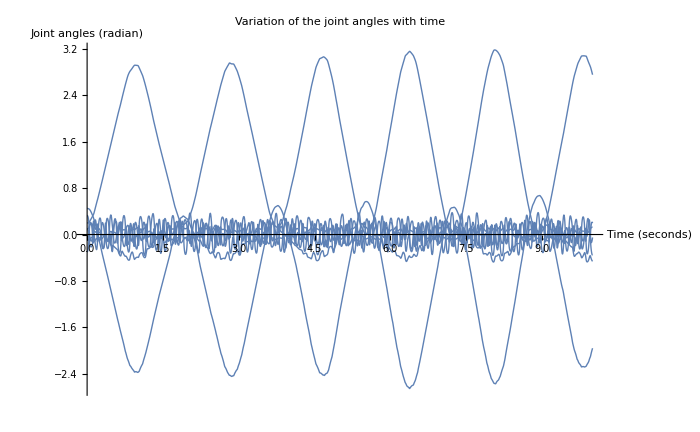

```mathematica
Plot[Evaluate[{z[t]}/.dynsim],{t,0,tf}, PlotRange-> All, PlotStyle->Thick, LabelStyle->Directive[Bold,Black,15], AxesLabel-> {"Time (seconds)","Joint angles (radian)"}, PlotLabel->"Variation of the joint angles with time",ImageSize->700]
```

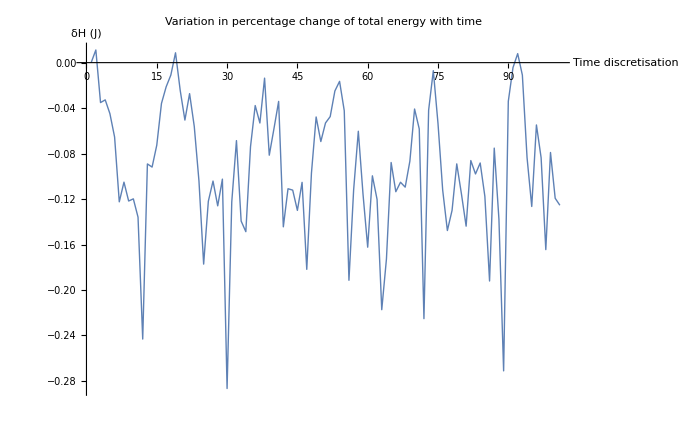

```mathematica
qdot = D[qt,t];
T = 1/2 *qdot.M.qdot;

H = T+(V/.q2qt);
δH = (H/(H/.{t-> 0})-1)*100/.numdata;
cH = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real},{θ5, _Real}, {θ6, _Real}, {θ7, _Real},  {dθ1, _Real}, {dθ2, _Real}, {dθ3, _Real}, {dθ4, _Real}, {dθ5, _Real}, {dθ6, _Real}, {dθ7, _Real}},Evaluate[H/.numdata/.dθ/.qt2q]];
Hi = cH@@Flatten[Join[{z[t]},{D[z[t], t]}]/.dynsim/.t->0];
ListLinePlot[Table[((cH@@Flatten[Join[{z[t]},{D[z[t], t]}]/.dynsim/.t->ii])/Hi)-1,{ii, 0, 10, 0.1}], PlotStyle->Thick, LabelStyle->Directive[Bold,Black,15], AxesLabel-> {"Time discretisation","δH (J)"}, PlotLabel->"Variation in percentage change of total energy with time",ImageSize->700]
```

```mathematica
Manipulate[robot/.Inner[Rule, θ, (z[t]/.dynsim/.t->u), List],{u, 0, 10}]
```

ReplaceAll::reps: {dynsim} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inner::heads: Heads ReplaceAll and List at positions 3 and 2 are expected to be the same.

ReplaceAll::reps: {Inner[Rule,{θ1,θ2,θ3,θ4,θ5,θ6,θ7},z[7.74]/.dynsim,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.